# Themis Control Overview

Goal: derive analytical expressions for theta_rms given some assumptions about mount and disturbances

## Model

Motor modelling: https://arxiv.org/pdf/2310.00080

Mechanical plant:

```mathematica
J ω s+b ω==KT i+τd
```

Electrical plant:

```mathematica
Solve[L i s+R i+KE ω==V,i]
```

{{i→(V-KE ω)/(R+L s)}}

There is a pole at s = - R/L, frequency ωe = R/L

Since ω is very small, the KE term can be neglected, and the gain from voltage to torque is thus

```mathematica
KT/(R+L s)=KT/R ωE/(s+ωE)
```

```mathematica
KT/R ωE/(s+ωE)/.{ωE->R/L}//FullSimplify
```

KT/(R+L s)

The transfer from voltage to current could benefit stabilisation

## Loops

## Current sensor

We want to get rid of the pole from voltage to torque:

```mathematica
GE=KT/R ωE/(s+ωE);
```

We introduce a PI with gain

```mathematica
GC=Kp (1+ωE/s);
```

The open loop gain is then

```mathematica
GL=GE*GC//FullSimplify
```

(Kp KT ωE)/(R s)

and the closed loop gain is (needs a torque measurement, which we proxy via a current measurement)

```mathematica
GL/(1+GL)/.{Kp->R ωci}//FullSimplify
```

(KT ωci ωE)/(s+KT ωci ωE)

PI for current regulation with closed-loop TF (assumption)

```mathematica
Iact/Icmd==ωci/(s+ωci)
```

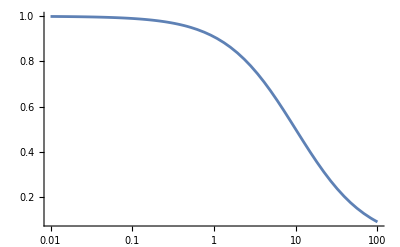

```mathematica
LogLinearPlot[10/(s+10),{s,0.01,100},PlotRange->All]
```

The gain between Icmd and motor torque production is then

```mathematica
GA==KT ωci/(s+ωci)
```

## No current sensor

Gain from voltage to torque is (as derived above)

```mathematica
KT/R ωE/(s+ωE)
```

So the voltage command better not be in this region, otherwise the tracking fails.
As a rule of thumb, ωcontrol = ωe/3